```mathematica
(*Define lengths of rectangular slab, area of cylindrical parallel wires and physical parameters*)
a=6;
```

```mathematica
b=8;
c=6.75;
xi1=-1.5;
```

```mathematica
eta1=4b/5;
xi2=1.5;
```

```mathematica
eta2=3b/5;
```

```mathematica
eta3=2b/5;
eta4=b/5;
```

```mathematica
r=.25;
```

```mathematica
area=Pi*r^2;
```

```mathematica
curr=10;
mu=1.26*10^-8;
(*Define function that maps a surface current to the cross-sectional areas of the wires*)
```

```mathematica
unit[x_,y_]:=If[(x-xi1)^2+(y-eta1)^2≤r^2 ,curr/area,0]+If[(x-xi2)^2+(y-eta1)^2≤r^2 ,-curr/area,0];
jz[x_,y_]:=Sum[If[(x-xi1)^2+(y-i)^2≤r^2,curr/(area),0],{i,-3,3,6/8}]+Sum[If[(x-xi2)^2+(y-j)^2≤r^2,-curr/(area),0],{j,-3,3,6/8}];
```

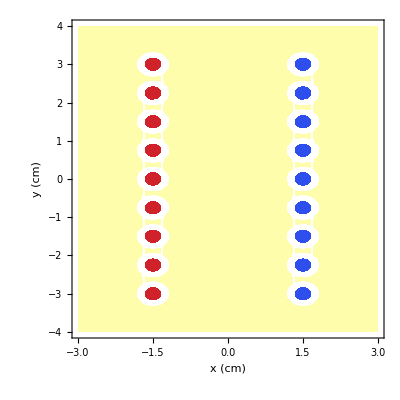

```mathematica
(*Plot the current function in the z-direction*)
ContourPlot[jz[x,y],{x,-a/2,a/2},{y,-b/2,b/2},FrameLabel->{"x (cm)","y (cm)"},PlotRange->All,ColorFunction->"TemperatureMap",PlotPoints->5]
```

```mathematica
(*Solving the PDE div(A)=-μJ for A, with  Dirichlet boundary conditions)
```

```mathematica
sol=NDSolve[{D[az[x,y,z],x,x]+D[az[x,y,z],y,y]+D[az[x,y,z],z,z]==-mu*jz[x,y],az[-a/2,y,z]==0,az[a/2,y,z]==0,az[x,-b/2,z]==0,az[x,b/2,z]==0,az[x,y,0]==0,az[x,y,c]==0},az,{x,-a/2,a/2},{y,-b/2,b/2},{z,0,c}]
```

{{az→InterpolatingFunction[{{-3., 3.}, {-4., 4.}, {0., 6.75}}, <>]}}

```mathematica
afield[x_,y_,z_]:=Evaluate[az[x,y,z]/.sol][[1]];
(*Plotting this solution for different values of height z*)
```

```mathematica
Manipulate[ContourPlot[afield[x,y,z],{x,-a/2,a/2},{y,-b/2,b/2},PlotRange->All,ColorFunction->"TemperatureMap"],{z,0,c}]
```

```mathematica
(*Calculating the magnetic field intensity H from A given μH=curl(A) *)
```

```mathematica
hx[x_,y_,z_]=(1/mu)*D[afield[x,y,z],y];
```

```mathematica
hy[x_,y_,z_]=-(1/mu)*D[afield[x,y,z],x];
```

```mathematica
h2[x_,y_,z_]=Sqrt[hx[x,y,z]^2+hy[x,y,z]^2];
```

```mathematica
(*Plotting the amplitude of H at z=c/2*)
```

```mathematica
ContourPlot[h2[x,y,c/2],{x,0,a},{y,0,b},PlotRange->All,ColorFunction->"TemperatureMap",PlotPoints->30,Contours->30,PlotLegends->Automatic]
```

-Graphics-

```mathematica
(*Plotting how the amplitude of H varies along the y axs if x=a/2,z=c/2*)
```

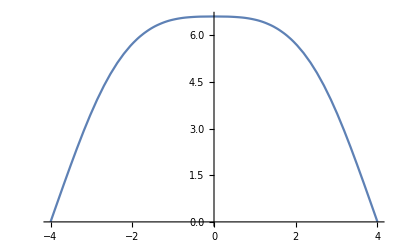

```mathematica
Plot[h2[a/2,y,c/2],{y,-b/2,b/2}]
```

```mathematica
(*Finding A with Neumann boundary conditions, and plotting it*)
```

```mathematica
sol2=NDSolve[{D[az[x,y,z],x,x]+D[az[x,y,z],y,y]+D[az[x,y,z],z,z]+mu*jz[x,y]==NeumannValue[0,-a/2≤x≤a/2]+NeumannValue[0,-b/2≤y≤b/2]+NeumannValue[0,-c/2≤z≤c/2]},az,{x,-a/2,a/2},{y,-b/2,b/2},{z,-c/2,c/2},AccuracyGoal->30,PrecisionGoal->30]
```

NDSolve::femibcnd: No DirichletCondition or Robin-type NeumannValue was specified for {az}; the result may not be unique.

{{az→InterpolatingFunction[{{-3., 3.}, {-4., 4.}, {-3.375, 3.375}}, <>]}}

```mathematica
cgauge[x_,y_,z_]:=Evaluate[az[x,y,z]/.sol2][[1]];
```

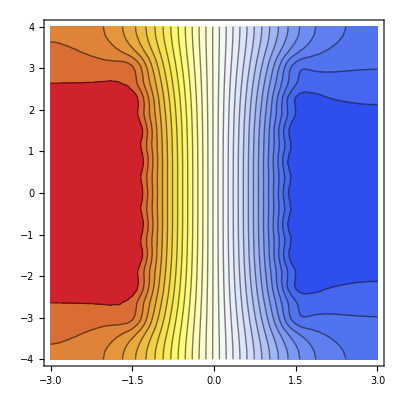

```mathematica
ContourPlot[cgauge[x,y,c/2],{x,-a/2,a/2},{y,-b/2,b/2},PlotRange->All,PlotPoints->20,Contours->30,ColorFunction->"TemperatureMap"]
```

```mathematica
(*Finding H from A*)
hxcg[x_,y_,z_]=(1/mu)*D[cgauge[x,y,z],y];
```

```mathematica
hycg[x_,y_,z_]=-(1/mu)*D[cgauge[x,y,z],x];
```

```mathematica
h2cg[x_,y_,z_]=Sqrt[hxcg[x,y,z]^2+hycg[x,y,z]^2];
```

```mathematica
(*Plotting the amplitude of H for fixed x=0, z=0*)
```

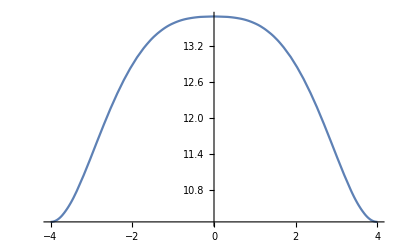

```mathematica
Plot[h2cg[0,y,0],{y,-b/2,b/2}]
```

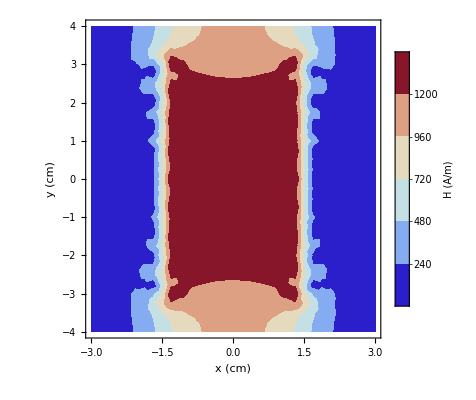

```mathematica
(*Plotting the amplitude of H for fixed z=0*)
ContourPlot[100*h2cg[x,y,0],{x,-a/2,a/2},{y,-b/2,b/2},PlotRange->All,FrameLabel->{"x (cm)","y (cm)"},ColorFunction->"ThermometerColors",PlotPoints->30,ContourStyle->None,Contours->5,PlotLegends->{LegendLabel->"H (A/m)"}]
```